```mathematica
Subscript[k, m]∙Subscript[i, a]+Subscript[T, f]=Subscript[I, m]∙Subscript[ω, m]∙s+Subscript[D, f]∙Subscript[ω, m]^2+Subscript[B, f]∙Subscript[ω, m]
```

```mathematica
Solve[km*ia-Tf==Im1*wm*s+Df *wm^2+Bf*wm,wm]//FullSimplify
```

{{wm→-(Bf+Im1 s-√((Bf+Im1 s)^2+4 Df (ia km-Tf)))/(2 Df)},{wm→-(Bf+Im1 s+√((Bf+Im1 s)^2+4 Df (ia km-Tf)))/(2 Df)}}

```mathematica
wm(-2 Df)==Bf+Im1 s-√((Bf+Im1 s)^2+4 Df (ia km-Tf))
```

```mathematica
(Subscript[K, m]/(Subscript[L, a]∙Subscript[I, m]∙s^2+(Subscript[L, a]∙B+Subscript[L, a]∙Subscript[D, fB]+Subscript[R, a]∙Subscript[I, m])s+Subscript[R, a](Subscript[B, f]+Subscript[D, fB])))/(1+((Subscript[K, m]∙Subscript[K, e])/(Subscript[L, a]∙Subscript[I, m]∙s^2+(Subscript[L, a]∙B+Subscript[L, a]∙Subscript[D, fB]+Subscript[R, a]∙Subscript[I, m])s+Subscript[R, a](Subscript[B, f]+Subscript[D, fB]))))//FullSimplify
```

K_m/(∙ K_e K_m+∙ s (B+∙ s ⅈ_m+D_(B f)) L_a+∙ s ⅈ_m R_a+R_a[B_f+D_(B f)])

```mathematica
(Km/(La * Im1 s^2 + (La Bf +La DfB +Ra Im1)s+Ra(Bf +DfB)))/(1+(Km Ke/(La * Im1 s^2 + (La Bf +La DfB +Ra Im1)s+Ra(Bf +DfB))))//FullSimplify
```

Km/(Ke Km+(Bf+DfB+Im1 s) (Ra+La s))

```mathematica
Km/(KeKm+(Bf+Im1s)(Ra+Las))
```

```mathematica
Subscript[T, f](Subscript[L, a]∙s+Subscript[R, a])/Subscript[K, m]
```

```mathematica
Tf=0.022;
La = 0.004;
Ra = 5.5;
Km = 0.3365;
Ke = 0.514;
Bf = 0.00051;
Im1 = 0.0005;
```

```mathematica
funktion=InverseLaplaceTransform[(10/s -(Tf*(La s+ Ra)/Km))*Km/(Ke Km +(Bf+Im1 s)(Ra+La s)),s,t];
```

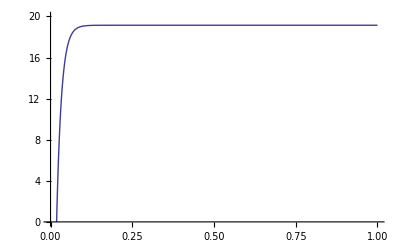

```mathematica
Plot[funktion,{t,0,1},PlotRange->{0,20}]
```

```mathematica
Tf=0.0547;
La = 0.024;
Ra = 69;
Km =1.38;
Ke = 0.00578;
Im1 = 0.0005;
DfB=1.35*10^-4;
DfT=0;
```

```mathematica
funktion=InverseLaplaceTransform[(10/s -((Tf-DfT)*(La s+ Ra)/Km))*Km/(Ke Km +(DfB+Im1 s)(Ra+La s)),s,t];
```

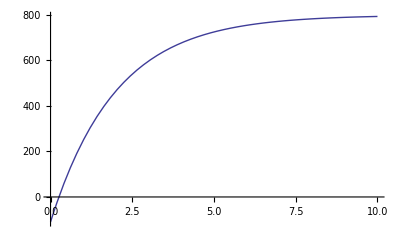

```mathematica
Plot[funktion,{t,0,10}]
```

```mathematica
Table[D[2*10^-7i^2],{i,0,4}]
```